```mathematica
link=Install[LinkConnect["38019@192.168.150.128,39391@192.168.150.128",LinkProtocol->"TCPIP"]]
```

LinkObject[…]

```mathematica
handle = With[
{c=15,Ωp=1.0,Ωe=-100,θr=0.45,θe=Sqrt[0.8],θb=0.045,ωb=14.2302,ωe=150,
ωp ={0.0292,
0.1255,
0.3348,
0.5943,
0.8157,
0.9857,
1.1176,
1.2200,
1.2972,
1.3513,
1.3833,
1.3939,
1.3833,
1.3513,
1.2972,
1.2200,
1.1176,
0.9857,
0.8157,
0.5943,
0.3348,
0.1255,
0.0292},
vd={1.90288,1.99424,2.025,1.99424,1.90288,1.7537,1.55124,1.30164,1.0125,0.692591,0.351638,0,-0.351638,-0.692591,-1.0125,-1.30164,-1.55124,-1.7537,-1.90288,-1.99424,-2.025,-1.99424,-1.90288},
vr={-0.692591,-0.351638,0,0.351638,0.692591,1.0125,1.30164,1.55124,1.7537,1.90288,1.99424,2.025,1.99424,1.90288,1.7537,1.55124,1.30164,1.0125,0.692591,0.351638,0,-0.351638,-0.692591}
},
dist=Join[
Thread[wstpDRingDistribution[Ωp,ωp,θr,θr,vd*2.2/2.025,vr*2.2/2.025]],
Thread[wstpDMaxwellianDistribution[{Ωp,Ωe},{ωb,ωe},{θb,θe}]]];
wstpDCreateDispersionObject[c,dist]];
```

```mathematica
check=With[{k=3.1,wna=84Degree},wstpDFindRoot[handle,k Cos[wna],k Sin[wna],Complex[3.0,0.05] (1+0.0001 I {0,1,2}),MaxIterations->100]];
```

{2.88284-0.00761121 ⅈ,2.8765-0.0022687 ⅈ,2.87051+0.00353667 ⅈ,2.86507+0.0100736 ⅈ,2.86062+0.0176876 ⅈ,2.85799+0.0266086 ⅈ,2.85861+0.0365843 ⅈ,2.86391+0.0461884 ⅈ,2.87369+0.0527884 ⅈ}

{2.88284-0.00761121 ⅈ,2.8765-0.0022687 ⅈ,2.87051+0.00353667 ⅈ,2.86507+0.0100736 ⅈ,2.86062+0.0176876 ⅈ,2.85799+0.0266086 ⅈ,2.85861+0.0365843 ⅈ,2.86391+0.0461884 ⅈ,2.87369+0.0527884 ⅈ,2.88621+0.0546894 ⅈ,2.8997+0.0515783 ⅈ,2.91249+0.0435748 ⅈ,2.92308+0.0316859 ⅈ,2.93135+0.0180532 ⅈ,2.93987+0.00476355 ⅈ,2.95171-0.00353648 ⅈ,2.96023-0.00406875 ⅈ,2.96437-0.00363234 ⅈ,2.96679-0.00341236 ⅈ,2.96837-0.00333075 ⅈ,2.96943-0.00332018 ⅈ,2.97016-0.00334705 ⅈ,2.97063-0.00339541 ⅈ,2.97092-0.00345705 ⅈ,2.97106-0.00352723 ⅈ,2.97108-0.00360263 ⅈ,2.97168-0.00403644 ⅈ}

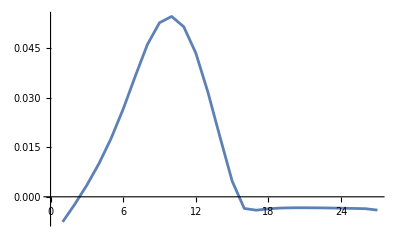

```mathematica
sol1=With[{k=Range[3.1,2.7,-0.05],wna=88Degree},wstpDFindRoot[handle,k Cos[wna],k Sin[wna],Complex[3.0,0.05] (1+0.0001 I {0,1,2}),MaxIterations->100]];
sol2=With[{k=Range[3.15,4.0,0.05],wna=88Degree},wstpDFindRoot[handle,k Cos[wna],k Sin[wna],Complex[3.0,0.05] (1+0.0001 I {0,1,2}),MaxIterations->100]];
sol1=Reverse[sol1[[2,2]]]
sol=Join[sol1,sol2[[2,2]]]
ListLinePlot[Im[sol]]
```

```mathematica
Export["vs=2.2-83-0.9h-0.09-im-3,2.7-4.0.csv",Im[sol]];

Export["vs=2.2-83-0.9h-0.09-re-3,2.7-4.0.csv",Re[sol]];
```